```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev0.dat"]//Flatten;
dat1=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev1.dat"]//Flatten;
dat2=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev2.dat"]//Flatten;
dat3=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev3.dat"]//Flatten;
dat4=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev4.dat"]//Flatten;
dat5=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/chebyshev4.dat"]//Flatten;

xval=Table[-1.0+0.01*i,{i,0,199}];
```

```mathematica
dat1//Length
xval//Length
```

200

200

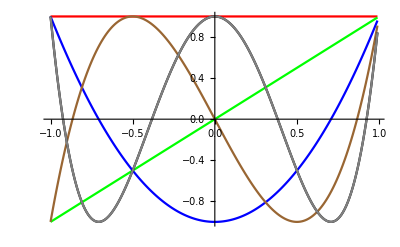

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}],
Transpose[{xval,dat1}],
Transpose[{xval,dat2}],
Transpose[{xval,dat3}],
Transpose[{xval,dat4}],
Transpose[{xval,dat5}]
}, PlotRange->All, PlotStyle->{Red, Green, Blue, Brown, Black, Gray}]
```